```mathematica
<<"C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\SpectraFitting.m"
```

Usage Instructions:

1. Get a list of spectra from a directory by using the GetSpecDir[path] function.

2. (Optional) Get an individual spectrum for flatfield correction using the GetSpec[path] function. Divide each spectrum by this flat-field using the SpecDivide[spec,ffspec] function.

3. Initialize a list of guesses using the CoordInit[Spectra,center,d] function, where center is a very preliminary guess for the center point of a generic spectrum and d is the overall spread to zoom in on for further fitting. You should save this guess as a variable.

4. Use the PickGuesses[Spectra,CoordList] command to interactively refine these guesses. CoordList should be the variable you defined in the previous step.

5. Run SingleLorentzianFit[Spectra, Coordlist] to fit each function to a single Lorentzian. Save the output to a variable. More options are coming soon.

6. Use the ShowFits[Spectra, CoordList, Fits, Path] where Fits is the list of fits and Path is the original directory to display all of the fits and important parameters.


If you need additional help, all of the functions have usage instructions that can be queried with two question marks and the name of the function, e.g. ??ShowFits .

## Data input and grooming

Directory where spectra reside. Should be tab separated files, but CSV will probably also work.

```mathematica
DataDir="C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS";
```

```mathematica
XPSPath="C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS\\2014-06-17_10048_76_77_79_synchotronsamples.xlsx";
```

```mathematica
XPSSpecs=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
sheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

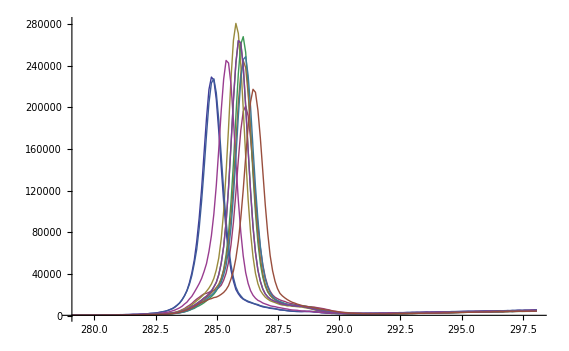

```mathematica
ListLinePlot[XPSSpecs,PlotRange->All]
```

```mathematica
coordlist=CoordInit[XPSSpecs,285,5]
```

{{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}}}

```mathematica
PickGuesses[XPSSpecs,coordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
coordlist
```

{{{285,1000},{280.7,1300.},{290.82,2600.},{290.28,2600.}},{{286.48,4000.},{565/2,1000},{292.01,2600.},{290.84,3000.}},{{285.94,3350.},{565/2,1000},{291.56,2250.},{290.61,2350.}},{{286.48,4100.},{565/2,1000},{291.29,2250.},{290.66,2250.}},{{284.86,3050.},{281.22,1200.},{291.11,2700.},{290.48,2450.}},{{285,1000},{281.49,1500.},{291.15,2250.},{290.43,2450.}},{{285.4,3100.},{565/2,1000},{291.38,2350.},{290.75,2000.}},{{285,1000},{565/2,1000},{291.29,2250.},{290.66,1950.}},{{286.25,6150.},{565/2,1000},{291.29,2300.},{290.43,2550.}},{{285,1000},{565/2,1000},{291.47,2450.},{290.79,2250.}},{{285,1000},{565/2,1000},{291.74,2500.},{290.88,2800.}}}

Pick one spectrum to work with.

```mathematica
data=ChopBoth[XPSSpecs,coordlist][[1]];
```

```mathematica
AllData=ChopBoth[XPSSpecs,coordlist];
```

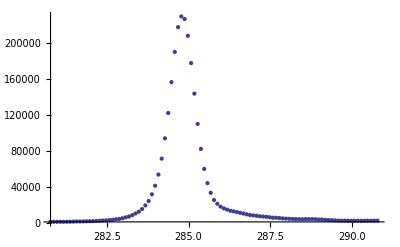

```mathematica
ListPlot[data,PlotRange->All]
```

## Peak fitting XPS data

### Fitting XPS data

#### Simple Fitting

Fit is not very good leaving everything free when the data are far from the origin. Note that the second gaussian is extremely far away from the first, so it has a negligible impact on the fit.

217426. ⅇ^(-2.99934 (-284.808+x)^2)+11142.2 ⅇ^(-5.97738×10^-6 (60.9918+x)^2)

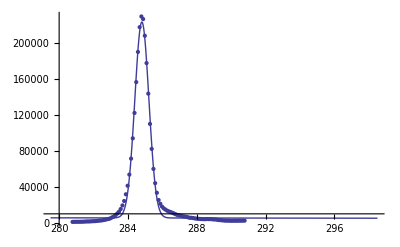

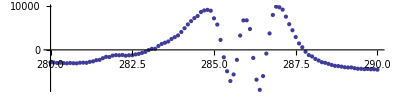

94.5379

```mathematica
nlm=Model[data,2];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"],AspectRatio->0.25,DataRange->{280,290}]
Print[nlm["FitResiduals"]//Total]
```

Centering and normalizing the data does much better. When Mathematica does its optmization routines, it assumes that all parameters are O(1), which means that it has to search a gigantic space. This situation can be somewhat alleviated by picking reasonable guesses (which is performed by Model[] automatically) but it seems that working with the normalized data is the best.

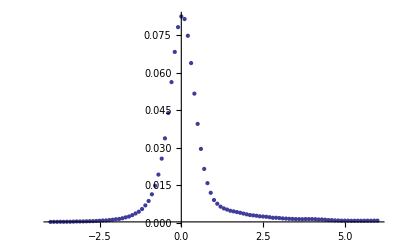

0.000890196 ⅇ^(-0.243997 (-4.93389+x)^2)+0.00479045 ⅇ^(-0.180594 (-0.551007+x)^2)+0.0542504 ⅇ^(-4.93188 (-0.0427552+x)^2)+0.0243921 ⅇ^(-1.6044 (0.0373253+x)^2)

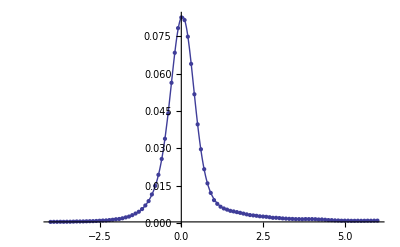

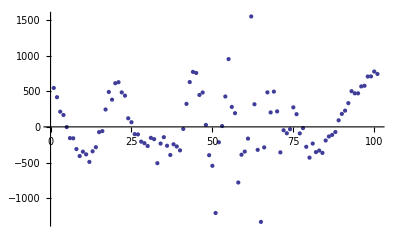

0.00104345

```mathematica
sdata=CenterAndNormalize[data];
ListPlot[sdata,PlotRange->All]
nlm=Model[sdata,4];
nlm[x]
Show[ListPlot[sdata,PlotRange->All],Plot[nlm["Function"][x],{x,-3,3},PlotRange->All]]
ListPlot[nlm["FitResiduals"]*Total[dataᵀ[[2]]]]
Print[(nlm["FitResiduals"]^2//Total)*(60.06/0.1511)]
```

Fit Residuals: 0.00156518

| Weights | Centers
Peak 1
Peak 2
Peak 3
Peak 4 | 0.731514
0.0415963
0.279766
0.0208425 | 0.
0.508252
-0.0800805
4.89113

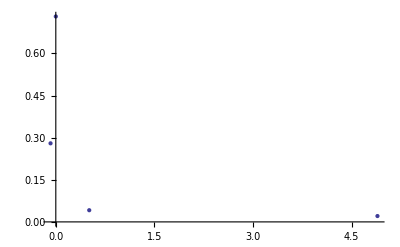

```mathematica
ListPlot[FitSummary[nlm]]
```

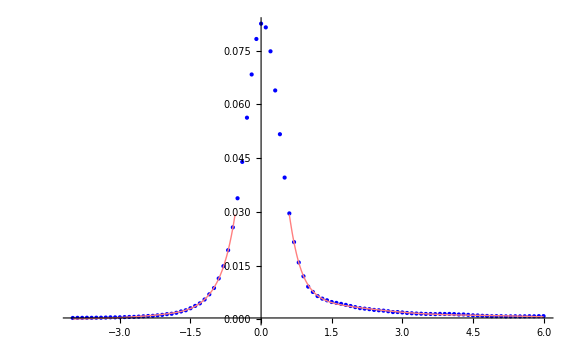
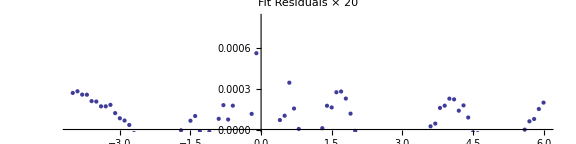

```mathematica
SummaryPlot[sdata,nlm]
```

We can see how the fit improves when adding more gaussians:

```mathematica
Fits=Table[Model[sdata,i],{i,1,6}];
```

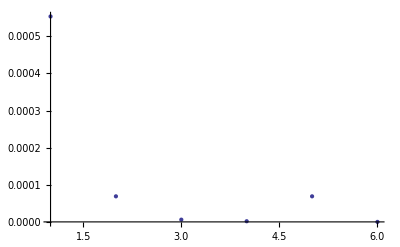

```mathematica
ListPlot[Table[Fits[[i]]["FitResiduals"]^2//Total,{i,1,6}],PlotRange->All]
```

#### Fitting with Voigt profiles (work in progress)

Can also use Voigt profiles. More parameters, trickier to fit. Prone to finding local minima. Not recommended yet.

(221494. 2^(-4.79661 (-284.803+x)^2))/(1-0.48443 (-284.803+x)^2)+(17836. 2^(-0.0489499 (-67.0585+x)^2))/(1-0.0451856 (-67.0585+x)^2)+(948.559 2^(-0.029004 (-20.4369+x)^2))/(1-0.0272774 (-20.4369+x)^2)

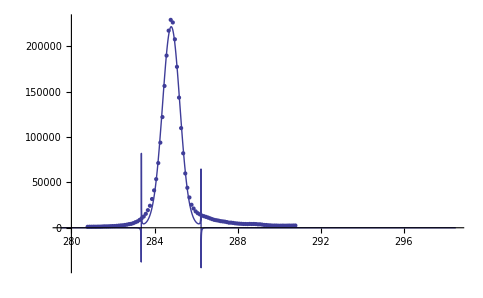

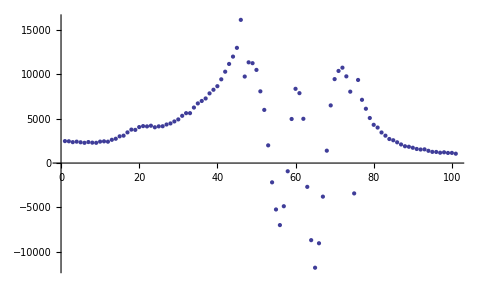

```mathematica
nlm=VoigtModel[data,3];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

#### Fitting by fixing peak positions

Can used knowledge of peak positions with FixedPeaksModel:

279.065 ⅇ^(-0.0000577052 (-288.102+x)^2)+444.521 ⅇ^(-0.0000112515 (-287.002+x)^2)+12323. ⅇ^(-0.128642 (-285.802+x)^2)+213264. ⅇ^(-3.24599 (-284.802+x)^2)

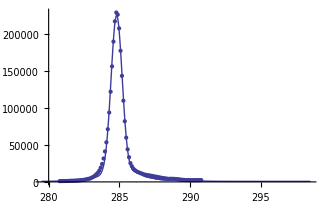

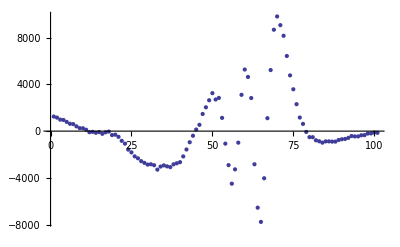

```mathematica
nlm=FixedPeaksModel[data,{-1,0,1.2,2.3}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

#### Fitting with fixed peaks voigt profile (work in progress)

Can used knowledge of peak positions with FixedPeaksModel:

(0.0248885 2^(0.0000582317 (-938.197+x)^2))/(1+0.0000593864 (-938.197+x)^2)

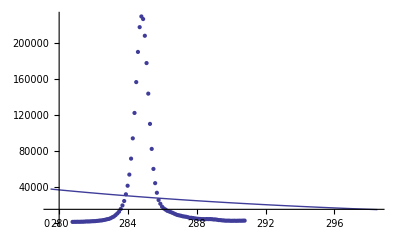

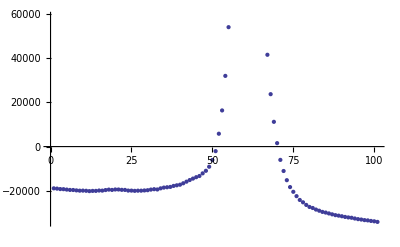

```mathematica
nlm=FixedPeaksVoigtModel[data,{0}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

(1066.75 2^(-60.6086 (-319.713+x)^2))/(1-60.5002 (-319.713+x)^2)+(1.07972×10^6 2^(-0.00330268 (-318.613+x)^2))/(1-0.0000242776 (-318.613+x)^2)+(4.24744×10^6 2^(-0.00451086 (-317.413+x)^2))/(1-0.0044639 (-317.413+x)^2)+(531686. 2^(-0.125433 (-316.413+x)^2))/(1-0.125212 (-316.413+x)^2)

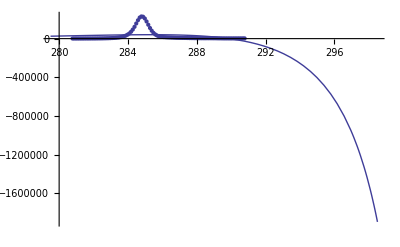

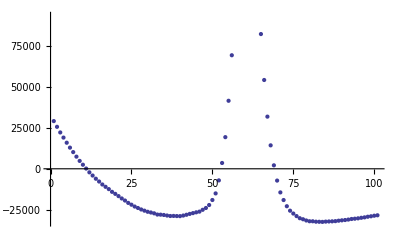

```mathematica
nlm=FixedPeaksVoigtModel[data,{-1,0,1.2,2.3}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

### Fitting example data

Example peak positions for a carbon 1s edge:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

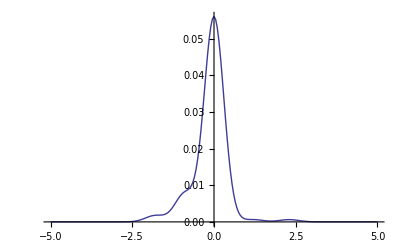

```mathematica
exweights={.10,.21,.57,.06,.06};
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[exweights[[i]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Try to fit this data with default values. It does a pretty good job, but misses the distinction between the peak at 1.2 and 2.3 eV.

Sum of squares of residuals: 1.1726286654736552e-6

{{0.236294,-0.000301534,-0.298856},{-0.0222503,1.57939,0.930734},{-0.00669281,-6.38624,-0.0542647},{0.087138,-0.897707,0.303996},{0.0413891,-1.80639,0.295499}}

{{0.835823,-0.000301534,-0.298856},{0.0230805,1.57939,0.930734},{0.000121753,-6.38624,-0.0542647},{0.115619,-0.897707,0.303996},{0.0253557,-1.80639,0.295499}}

Weights | Means | σs
0.835823 | -0.000301534 | -0.298856
0.0230805 | 1.57939 | 0.930734
0.000121753 | -6.38624 | -0.0542647
0.115619 | -0.897707 | 0.303996
0.0253557 | -1.80639 | 0.295499

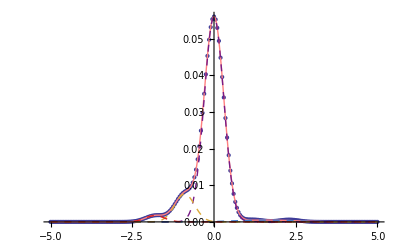

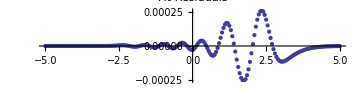

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Perfect results can be obtained by lowering the scaling factor.

Sum of squares of residuals: 1.4818850581755128e-15

{{-0.087135,-0.9,0.3},{0.0248956,2.3,-0.300003},{-0.0414929,-1.8,-0.299999},{-0.0248957,1.19999,-0.300002},{0.236509,-2.74128×10^-8,-0.3}}

{{0.11419,-0.9,0.3},{0.00932165,2.3,-0.300003},{0.0258933,-1.8,-0.299999},{0.00932163,1.19999,-0.300002},{0.841274,-2.74128×10^-8,-0.3}}

Weights | Means | σs
0.11419 | -0.9 | 0.3
0.00932165 | 2.3 | -0.300003
0.0258933 | -1.8 | -0.299999
0.00932163 | 1.19999 | -0.300002
0.841274 | -2.74128×10^-8 | -0.3

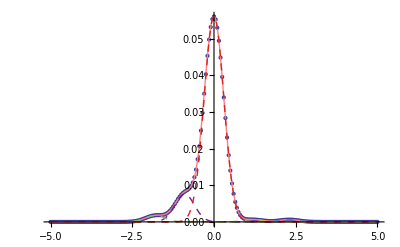

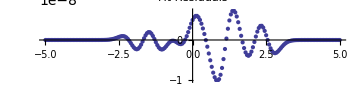

```mathematica
ExCModel=Model[ExampleCData,5,0.75];
FitSummary[ExampleCData,ExCModel];
```

## Fit all data quickly

### Carbon Peak

```mathematica
RawCData=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
CSheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

```mathematica
Ccoordlist=CoordInit[RawCData,285,8];
```

```mathematica
PickGuesses[RawCData,Ccoordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
CData=UserRemoveAve[RawCData,Ccoordlist];
```

```mathematica
CenteredCData=CenterAndNormalize/@CData;
```

```mathematica
AllCModels=FixedPeaksModel[#,{-1.8,-0.9,0,1.2,2.3}]&/@CenteredCData;
```

```mathematica
AllCModels=Model[#,5]&/@CenteredCData;
```

$Aborted

Weights | Means | σs
0.502163 | 0. | -0.393452
0.193079 | -0.321214 | -0.639077
0.167197 | -0.0258621 | 0.270023
0.129044 | 0.847527 | 1.10653
0.00851705 | 3.67551 | 0.641017

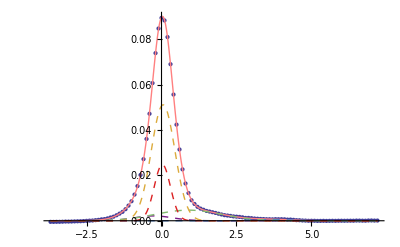

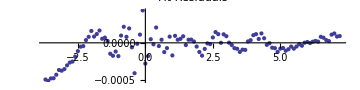

Weights | Means | σs
0.36077 | 0. | -0.312263
0.326821 | 0.0499375 | 0.49086
0.199502 | 0.997759 | 1.65675
0.108022 | -1.43291 | 0.647452
0.00488563 | 5.61451 | 0.569644

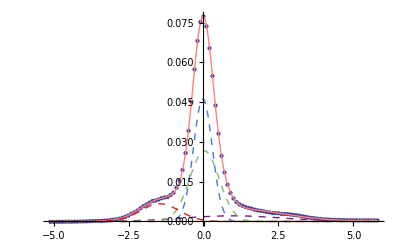

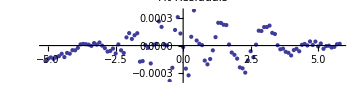

Weights | Means | σs
0.583476 | 0. | -0.330421
0.311156 | -0.197785 | -0.933161
0.0406276 | -0.0457451 | 0.196103
0.0362981 | 2.39366 | 0.749628
0.0284422 | 2.06449 | -2.84066

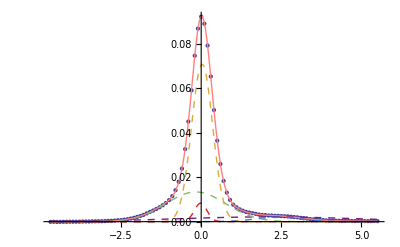

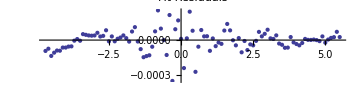

Weights | Means | σs
0.636034 | 0. | 0.317308
0.195013 | -0.331167 | -0.75263
0.151214 | 0.867185 | -1.52395
0.0177379 | 0.613191 | 0.24064
1.81365×10^-13 | 0.339039 | -0.868875

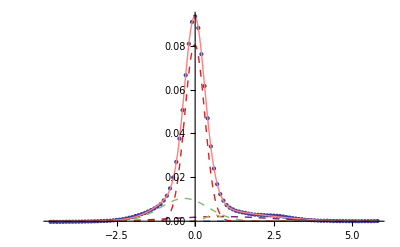

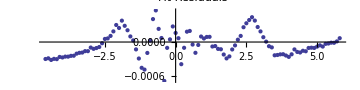

Weights | Means | σs
0.495283 | 0. | -0.317204
0.368909 | -0.139904 | -0.60886
0.130282 | 0.936908 | 1.40429
0.00524143 | 0.565763 | 0.157058
0.000284816 | 0.181505 | 0.00759614

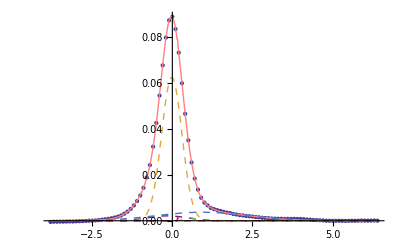

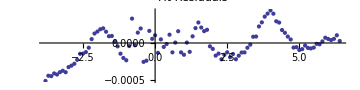

Weights | Means | σs
0.538016 | 0. | -0.315078
0.361657 | -0.279125 | 0.724445
0.100327 | 0.881968 | 1.47682
1.14429×10^-15 | 0.959194 | 0.817328
7.55574×10^-16 | 4.42926 | -1.34908

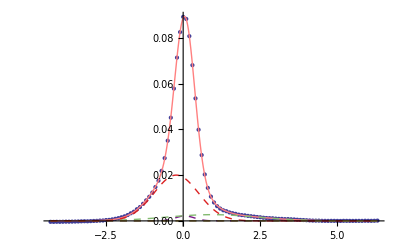

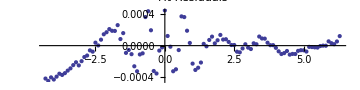

Weights | Means | σs
0.603327 | 0. | 0.323038
0.29521 | -0.321949 | 0.914453
0.0586584 | 0.826328 | 1.08336
0.028315 | 2.56718 | -0.642375
0.0144898 | 0.549855 | -0.222288

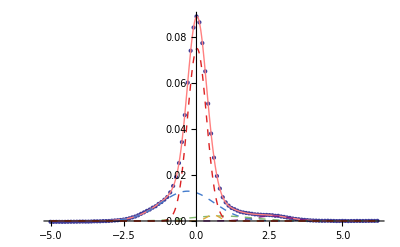

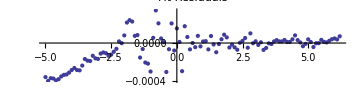

Weights | Means | σs
0.622004 | 0. | -0.321142
0.335437 | -0.117949 | -0.947125
0.0271109 | 2.69099 | -0.599665
0.00840717 | 2.03366 | -0.381547
0.00704108 | -0.984275 | -0.00356554

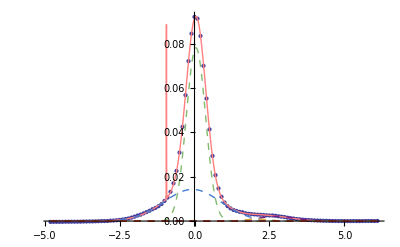

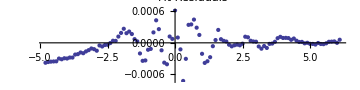

Weights | Means | σs
0.618906 | 0. | 0.331253
0.347954 | -0.139507 | 0.985289
0.0331402 | 2.54797 | -0.611437
7.35743×10^-15 | 0.741497 | -4.98402
3.82652×10^-16 | 1.20822 | -0.284046

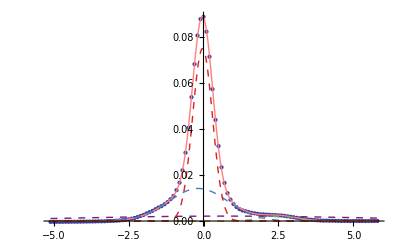

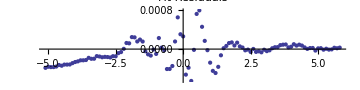

Weights | Means | σs
0.623061 | 0. | -0.321322
0.336022 | -0.118845 | -0.95123
0.0228979 | 2.79311 | -0.626146
0.0134699 | 2.15498 | -0.449327
0.00454912 | -1.19872 | -0.00310137

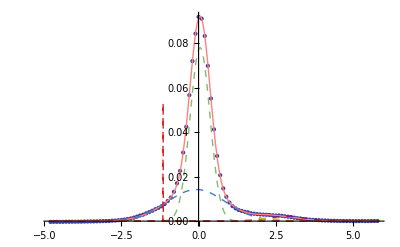

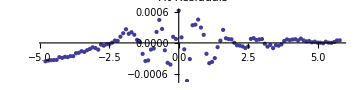

Weights | Means | σs
0.516189 | 0. | 0.339005
0.305201 | -0.157645 | 0.654456
0.117923 | 1.1291 | 1.24577
0.0606862 | -1.86101 | -0.564356
4.89588×10^-12 | 1.00851 | 2.42905

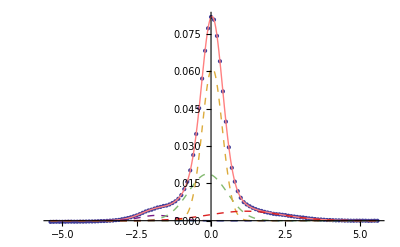

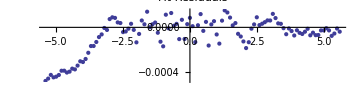

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]]],{x,1,Length[CenteredCData],1}];
```

Visualize location of peaks and weights:

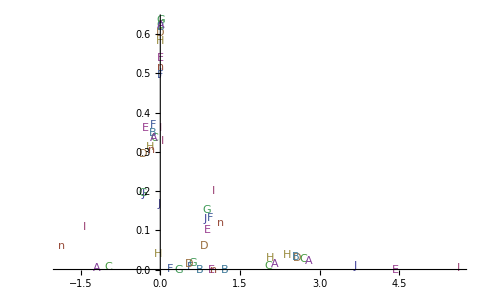

```mathematica
ComparePeaks[CSummaries,CSheets]
```

### Oxygen Peak

```mathematica
RawOData=GetSpec[XPSPath,"Excel XPS","O1s"];
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

11 spectra in all.

Importing Sheet O1s Scan J

Importing Sheet O1s Scan I

Importing Sheet O1s Scan H

Importing Sheet O1s Scan G

Importing Sheet O1s Scan F

Importing Sheet O1s Scan E

Importing Sheet O1s Scan D

Importing Sheet O1s Scan C

Importing Sheet O1s Scan B

Importing Sheet O1s Scan A

Importing Sheet O1s Scan

Formatting XPS Spectra

```mathematica
OSheets=GetSheets[XPSPath,"O1s"]
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

```mathematica
Ocoordlist=CoordInit[RawOData,532.5,7,12000]
```

{{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}}}

```mathematica
PickGuesses[RawOData,Ocoordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
OData=UserRemoveAve[RawOData,Ocoordlist];
```

```mathematica
CenteredOData=CenterAndNormalize/@OData;
```

Fitting works better if the fitting parameters are tweaked a little.

```mathematica
AllOModels=Model[#,4,0.7,0.1]&/@CenteredOData;
```

Weights | Means | σs
0.874396 | 0. | -0.742735
0.118266 | 1.46439 | 0.505756
0.00733787 | 0.730778 | 0.202887
2.38909×10^-15 | 1.22805 | -0.0557857

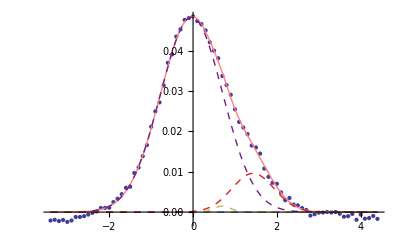

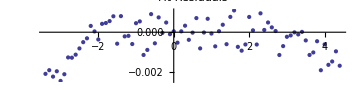

Weights | Means | σs
0.837196 | 0. | 0.828332
0.125163 | -1.26161 | 0.513958
0.0376415 | -2.2437 | -0.524787
1.09389×10^-15 | 7.28843 | 1.13965

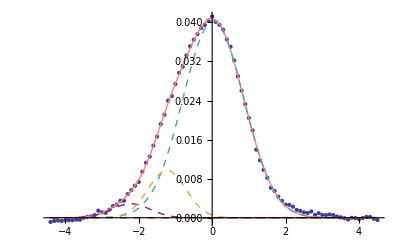

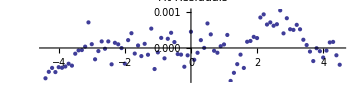

Weights | Means | σs
0.653603 | 0. | -0.884188
0.346397 | 0.357317 | -0.52724
1.05667×10^-15 | 2.5096 | 0.766575
7.45861×10^-16 | -0.23765 | 0.512961

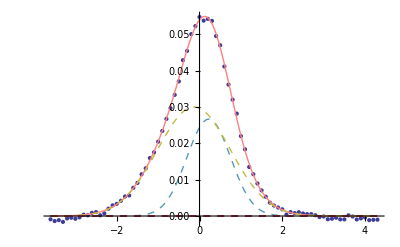

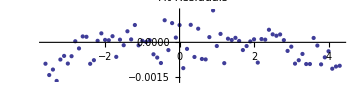

Weights | Means | σs
0.776322 | 0. | -0.873546
0.209321 | 0.324272 | -0.453076
0.0110191 | -2.00676 | -0.375741
0.00333731 | 0.990021 | 0.0838162

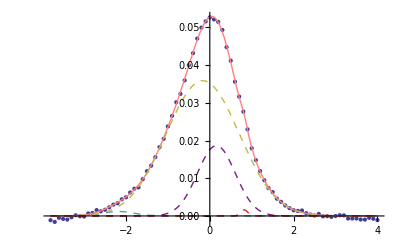

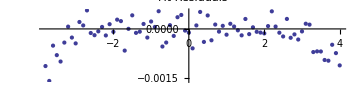

Weights | Means | σs
0.534729 | 0. | 0.941181
0.348729 | 4.44663 | -0.111634
0.116542 | -0.561733 | -0.540562
7.39575×10^-14 | -1.26733 | -1.66903

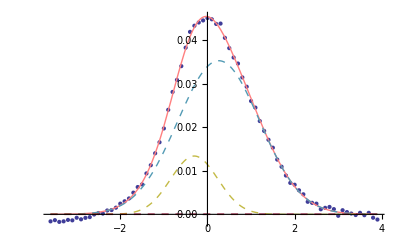

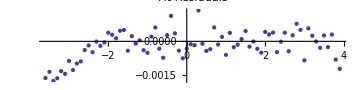

Weights | Means | σs
0.973399 | 0. | -0.879313
0.0192061 | 0.423804 | 0.40934
0.0073945 | -1.88311 | 0.30123
2.87036×10^-15 | -3.6756 | 2.07797

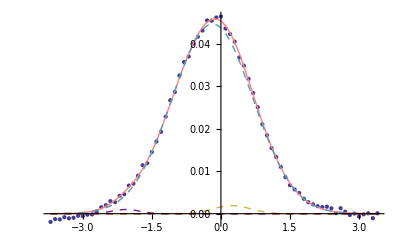

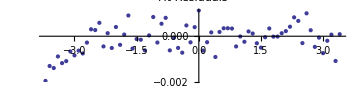

Weights | Means | σs
0.773084 | 0. | -0.923937
0.213826 | 0.413824 | 0.482582
0.00824337 | -2.26355 | -0.406699
0.00484642 | 2.62401 | -0.40358

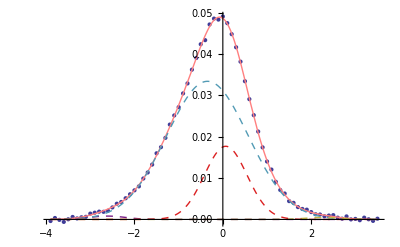

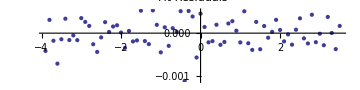

Weights | Means | σs
0.852568 | 0. | -0.806482
0.0785695 | 0.273038 | 0.385294
0.0688621 | -1.58587 | 0.637021
2.53352×10^-11 | -1.22528 | 1.09366

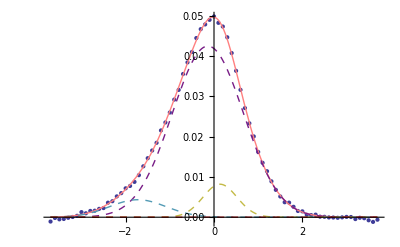

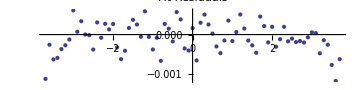

Weights | Means | σs
0.702948 | 0. | -0.919186
0.291838 | 0.446328 | 0.551286
0.00336372 | 0.48207 | -0.0744654
0.00184975 | -0.0628031 | 0.0283305

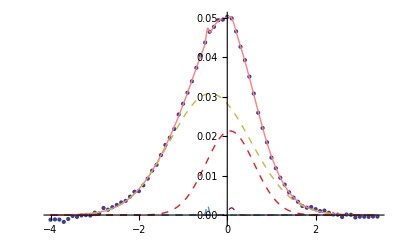

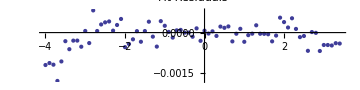

Weights | Means | σs
0.888669 | 0. | -0.722229
0.0680254 | -1.84434 | 0.530839
0.043306 | -1.19196 | 0.345794
1.55702×10^-15 | -0.987686 | -1.7759

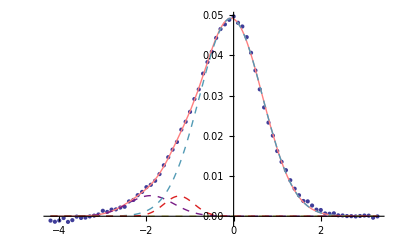

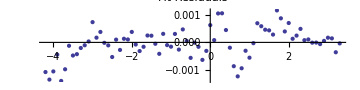

Weights | Means | σs
0.841105 | 0. | 0.969829
0.151044 | 0.784281 | -0.489246
0.0078509 | -2.1727 | -0.36118
4.66842×10^-14 | 0.20277 | -0.484569

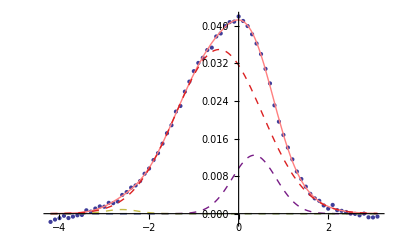

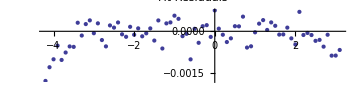

```mathematica
OSummaries=Table[FitSummary[CenteredOData[[x]],AllOModels[[x]]],{x,1,Length[CenteredOData]}];
```

Visualize location of peaks and weights:

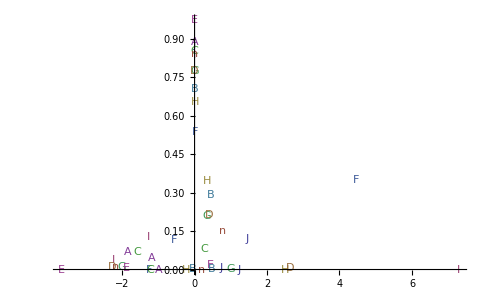

```mathematica
ComparePeaks[OSummaries,OSheets]
```

#### Oxygen Edge

## Multi-peak fitting with generated data

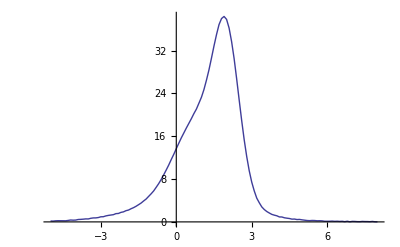

25.1057 ⅇ^(-1.99508 (-1.99902+x)^2)+16.1163 ⅇ^(-0.497021 (-0.990415+x)^2)+3.85703 ⅇ^(-0.116134 (-0.489983+x)^2)

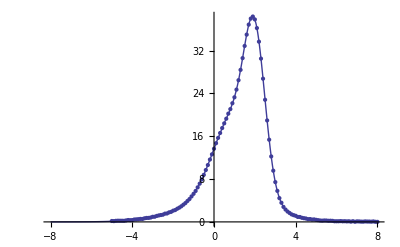

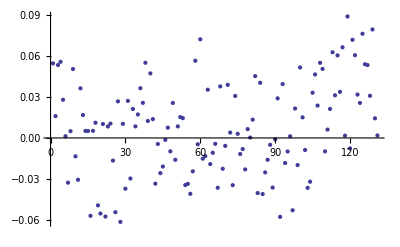

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=Model[data2,3];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```

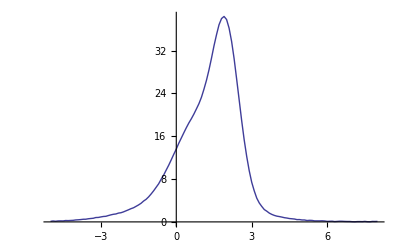

24.9801 ⅇ^(-2.01044 (-1.99924+x)^2)+16.1531 ⅇ^(-0.495882 (-0.99924+x)^2)+3.91041 ⅇ^(-0.118018 (-0.49924+x)^2)

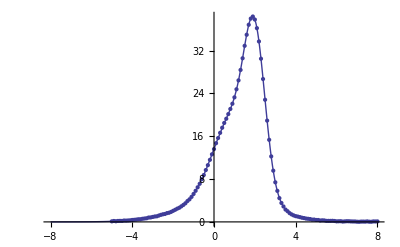

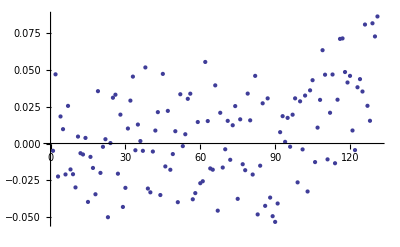

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=FixedPeaksModel[data2,{1,-0.5,0}];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```

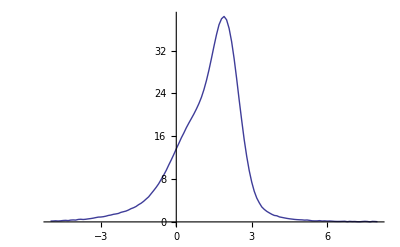

(33.4066 2^(-2.2467 (-1.90903+x)^2))/(1-0.135812 (-1.90903+x)^2)+(1.57346×10^-11 2^(-0.0664325 (-0.909032+x)^2))/(1+0.0354018 (-0.909032+x)^2)+(16.4409 2^(-0.0474042 (-0.409032+x)^2))/(1+1.00537 (-0.409032+x)^2)

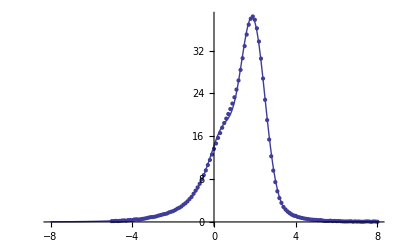

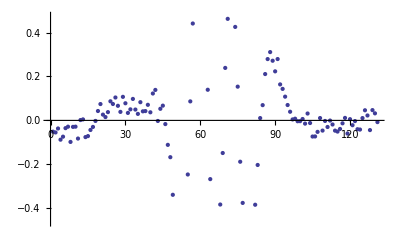

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=FixedPeaksVoigtModel[data2,{1,-0.5,0}];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```